```mathematica
h[x_]:=Piecewise[{{1+Subscript[c, 0,1] x+Subscript[c, 0,2] x^2, 0≤x≤1}, {Subscript[c, 1,1](x-1)+Subscript[c, 1,2](x-1)^2, 1<x≤2}, {0, True}}];
f[x_]:=h[Abs[x]];
AllVars={Subscript[c, 0,1],Subscript[c, 0,2],Subscript[c, 1,1],Subscript[c, 1,2]};
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
```

1+c_(0,1)+c_(0,2)

c_(1,1)+c_(1,2)

```mathematica
(*Partition of unity and linear term*)
T0=CoefficientList[FullSimplify[∑_(k=-1)^2 f[x-k],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[∑_(k=-1)^2 k f[x-k],x>0&&x<1],x]
```

{2+c_(0,1)+c_(0,2)+c_(1,1)+c_(1,2),-2 c_(0,2)-2 c_(1,2),2 c_(0,2)+2 c_(1,2)}

{1+c_(0,1)+c_(0,2)+2 c_(1,1)+2 c_(1,2),-c_(0,1)-2 c_(0,2)-3 c_(1,1)-4 c_(1,2),c_(0,2)+c_(1,2)}

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0
	},
	AllVars
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c_(0,2)→-1-c_(0,1),c_(1,1)→-1-c_(0,1),c_(1,2)→1+c_(0,1)}}

```mathematica
RegionXY[k_]:={Quotient[k,2],1+Quotient[-k,2]};
Regions=Table[RegionXY[k],{k,-2,5}]
```

{{-1,2},{-1,1},{0,1},{0,0},{1,0},{1,-1},{2,-1},{2,-2}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
W[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF=∑_(i=-3)^5 ∑_(j=-3)^5 W[i-j]f[x-i,y-j]/.GenSol;
SimplifySquare[f_,x0_,y0_]:=Simplify[f,x>x0&&x<x0+1&&y>y0&&y<y0+1];
DSimplifySquare[f_,{x0_,y0_}]:=Simplify[D[SimplifySquare[f,x0,y0],{{x,y}}]];
DSumF=ParallelMap[DSimplifySquare[SumF,#]&,Regions];
```

```mathematica
AnisoInt[df_,{x0_,y0_}]:=Simplify[Integrate[Expand[(df.{1,1})^2],{x,x0,x0+1},{y,y0,y0+1}]];
AnisoInts=Parallelize[MapThread[AnisoInt,{DSumF,Regions}]];
Err=Simplify[Total[AnisoInts]/.φ->1/2]
```

(752+2611 c_(0,1)+3192 c_(0,1)^2+1334 c_(0,1)^3+196 c_(0,1)^4)/1440

```mathematica
FreeVars=Variables[Err];
DErr=Simplify[D[Err,{FreeVars}]];
H=D[DErr,{FreeVars}];
Sols=RootReduce[Solve[DErr==0,FreeVars,Reals]];
RootReduce[Sols[[1]]]
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

{c_(0,1)→Root[2611+6384 #1+4002 #1^2+784 #1^3&,1]}

1 | 0.0494532 | True

{c_(0,2)→-0.378087,c_(1,1)→-0.378087,c_(1,2)→0.378087,c_(0,1)→-0.621913}

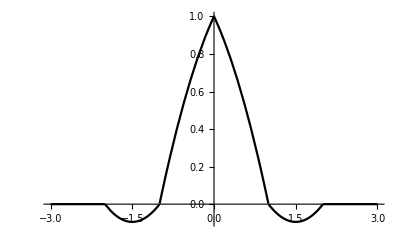

```mathematica
NSol=N[Sols[[1]]];
FullSol=Join[GenSol/.NSol,NSol]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```